### Conditions: 2 t_1 t_2 t_3=1 and r_2=r_1 t_2

(1-t_2^2)=r_1^2 t_2^2
1/((1+r_1^2)^(1/2))=t_2=1/((2-t_1^2)^(1/2))

2 t_1 1/((2-t_1^2)^(1/2))t_3=1
4 t_1^2/(2-t_1^2)t_3=1

```mathematica
t1[t3_]=√(2/(4 t3^2+1))
```

√2 √(1/(1+4 t3^2))

```mathematica
t2 [t3_]= 1/(√(2-t1[t3]^2))
```

1/(√(2-2/(1+4 t3^2)))

```mathematica
t3=N[1/2]
```

0.5

```mathematica
{t1[1/(√2)],t2[1/√2]}
```

{√(2/3),(√3)/2}

```mathematica
√(1-3/4)
```

1/2

```mathematica
N[1/(2 √2)]
```

0.353553

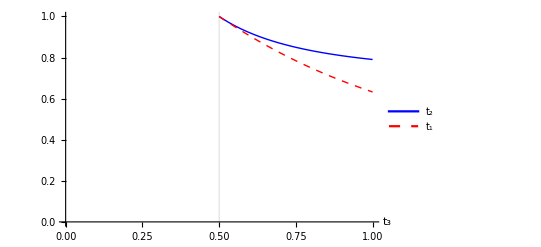

```mathematica
Plot[{t2[t3],t1[t3]},{t3,0,1},PlotRange->{0,1},PlotLegends->Placed[{"t_2","t_1"},{0.25,0.8}],AxesLabel->{"t_3"},LabelStyle->Large,GridLines->{{0.5},None},PlotStyle->{{Blue,Thick},{Red,Dashed,Thick}},AxesStyle->{{Thick,Black},{Thick,Black}}]
```

```mathematica
N[1/√2]
```

0.707107

```mathematica
FindMaximum[{√((1-t2[t3]^2)(1-t3^2)),0≤ t3≤1},{t3,0.6}]
```

{0.353553,{t3→0.707107}}

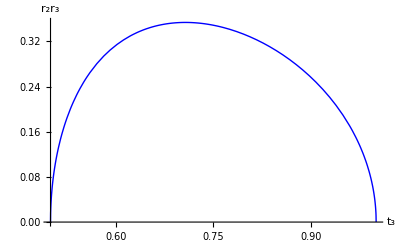

```mathematica
Plot[√((1-t2[t3]^2)(1-t3^2)),{t3,0.5,1},PlotRange->Full,GridLines->{{1/√2},{√((1-t2[1/√2]^2)(1-1/2))}},LabelStyle->Large,AxesLabel->{"t_3","r_2r_3"},AxesStyle-> {{Thick,Black},{Thick,Black}},ImageSize->Scaled[0.5],PlotStyle->{Thick,Blue}]
```

## Weak coherent state vs. qubit

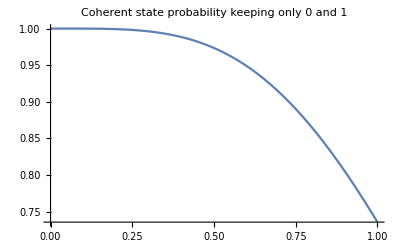

```mathematica
Plot[ⅇ^(-α^2)(1+α^2),{α,0,1},PlotLabel-> "Coherent state probability keeping only 0 and 1"]
```

#### Conclusion: α<0.4 coherent state seem to good approximation for qubit

### Comparing Wigner distributions

#### Wigner of Qubit

```mathematica
ClearAll[x,p]
ψn[n_,x_]=(ⅇ^(-x^2/2))/(π^(1/4)√(n!2^n))HermiteH[n,x];
ψ[β_,x_]=(√(1-β^2)ψn[0,x]+β ψn[1,x])/(√2)+(√(1-β^2)ψn[0,x]-β ψn[1,x])/(√2);
WQubit[β_,x_,p_]:=1/(2π)NIntegrate[ⅇ^(ⅈ p y)Conjugate[(ψ[β,x-1/2 y])] ψ[β,x+1/2 y],{y,-50,50}];
CatExact[α_,x_,p_]:=(ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)
limits=0.5;
range=15;
β=0.4;
matQubit=Table[Re[Chop[WQubit[β,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
ListPlot3D[matdata,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,InterpolationOrder->2,ImageSize->Large]
matCat=Table[Re[Chop[CatExact[β,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
ListPlot3D[matCat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,InterpolationOrder->2,ImageSize->Large]
```

-Graphics3D-

-Graphics3D-

## C-π/2

```mathematica
ClearAll[α,γ,ϕ,t2,t3]
PD[α_,γ_,ϕ_,t2_,t3_]=0.18082(1-t2^2)(1-t3^2)(1+2(α^2 Re[γ √(1-γ^2)ⅇ^(ⅈ ϕ)]+(1-α^2)Re[ⅈ  γ √(1-γ^2)ⅇ^(ⅈ ϕ)]));
```

```mathematica
Average= (∫_0^1 ∫_0^1 ∫_0^(2π) Simplify[PD[α,γ,ϕ,(√3)/2,1/√2]]ⅆϕⅆγⅆα)/(2π)
```

(∫_0^(2 π) (0.0226025-0.0100456 Im[ⅇ^(ⅈ ϕ)]+0.00502278 Re[ⅇ^(ⅈ ϕ)])ⅆϕ)/(2 π)

```mathematica
0.18082^2
```

0.0326959

```mathematica
Plot3D[ PD[α,γ,0,√3/2,1/(√2)],{α,0,1},{γ,0,1},LabelStyle->Large,AxesStyle->{{Thick,Black},{Thick,Black},{Thick,Black}}, PlotRange->Automatic,ImageSize->Large,Mesh->None,AxesLabel->{"α","γ","P_D"},ColorFunction->"Rainbow",PlotStyle->Opacity[0.8]]
```

```mathematica
Plot3D[ PD[α,γ,π/2,(√3)/2,1/(√2)],{α,0,1},{γ,0,1},LabelStyle->Large,AxesStyle->{{Thick,Black},{Thick,Black},{Thick,Black}}, PlotRange->Automatic,ImageSize->Large,Mesh->None,AxesLabel->{"α","γ","P_D"},ColorFunction->"Rainbow",PlotStyle->Opacity[0.8]]
```

-Graphics3D-

```mathematica
FindMaximum[{PD[α,γ,ϕ,(√3)/2,1/(√2)],α≥0&&α≤ 1&&γ≥ 0&&γ≤ 1&&ϕ≥ 0&&ϕ<2π},{α,γ,ϕ}]
```

{0.0301362,{α→0.999997,γ→0.707105,ϕ→0.00661122}}

```mathematica
FindMaximum[{PD[α,γ,0,(√3)/2,1/(√2)],α≥0&&α≤ 1&&γ≥ 0&&γ≤ 1},{α,γ}]
```

{0.0452049,{α→0.999998,γ→0.707106}}

## C-π

```mathematica
0.25 (1-1/2)(1-3/4)
```

0.03125

```mathematica
ClearAll[α,γ,ϕ,t2,t3]
PD[α_,γ_,ϕ_,t2_,t3_]=0.25(1-t2^2)(1-t3^2)(1+2(α^2-(1-α^2))Re[γ √(1-γ^2)ⅇ^(ⅈ ϕ)]);
```

```mathematica
Average= (∫_0^1 ∫_0^1 ∫_0^(2π) PD[α,γ,ϕ,√3/2,1/(√2)]ⅆϕⅆγⅆα)/(2π)
```

(∫_0^(2 π) (0.03125-0.00694444 Re[ⅇ^(ⅈ ϕ)])ⅆϕ)/(2 π)

```mathematica
(∫_0^(2 π) (0.03125-0.006944444444444444 Cos[ϕ])ⅆϕ)/(2 π)
```

0.03125

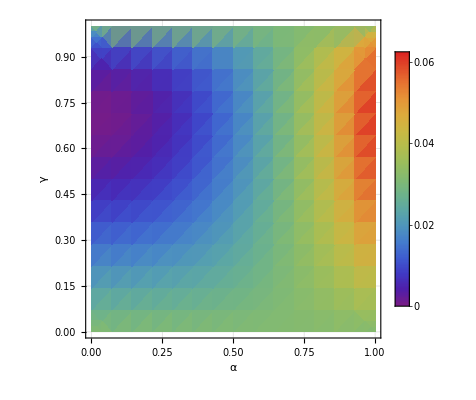

```mathematica
DensityPlot[PD[α,γ,0,(√3)/2,1/(√2)],{α,0,1},{γ,0,1},FrameLabel->Automatic,RotateLabel-> True,LabelStyle->Large,AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotRange->Full,ImageSize->Scaled[0.5],ColorFunctionScaling->True,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```

```mathematica
Plot3D[ PD[α,γ,0,(√3)/2,1/(√2)],{α,0,1},{γ,0,1},LabelStyle->Large,AxesStyle->{{Thick,Black},{Thick,Black},{Thick,Black}}, PlotRange->Automatic,ImageSize->Large,Mesh->None,AxesLabel->{"α","γ","P_D"},ColorFunction->"Rainbow",PlotStyle->Opacity[0.8]]
```

```mathematica
Plot3D[ PD[α,γ,π/2,(√3)/2,1/√2],{α,0,1},{γ,0,1},LabelStyle->Large,AxesStyle->{{Thick,Black},{Thick,Black},{Thick,Black}}, PlotRange->Automatic,ImageSize->Large,Mesh->None,AxesLabel->{"α","γ","P_D"},ColorFunction->"Rainbow",PlotStyle->Opacity[0.8]]
```

-Graphics3D-

```mathematica
Plot3D[ PD[α,γ,π,(√3)/2,1/(√2)],{α,0,1},{γ,0,1},LabelStyle->Large,AxesStyle->{{Thick,Black},{Thick,Black},{Thick,Black}}, PlotRange->Automatic,ImageSize->Large,Mesh->None,AxesLabel->{"α","γ","P_D"},ColorFunction->"Rainbow",PlotStyle->Opacity[0.8]]
```

-Graphics3D-

```mathematica
PD[0,0.5,π/2,(√3)/2,1/(√2)]
```

0.03125

```mathematica
FindMaximum[{PD[α,γ,ϕ,(√3)/2,1/(√2)],α≥0&&α≤ 1&&γ≥ 0&&γ≤ 1&&ϕ≥ 0&&ϕ<2π},{α,γ,ϕ}]
FindMaximum[{PD[α,γ,0,(√3)/2,1/(√2)],α≥0&&α≤ 1&&γ≥ 0&&γ≤ 1},{α,γ}]
```

{0.0624998,{α→0.999999,γ→0.707106,ϕ→0.00262628}}

{0.0624999,{α→0.999999,γ→0.707106}}

```mathematica
N[1/√2]
```

0.707107

## Gate Transformation

```mathematica
X=π;
PNSG=0.25;
(*β=√(1-α^2)ⅇ^(ⅈ Subscript[ϕ, T]);
δ=√(1-γ^2)ⅇ^(ⅈ Subscript[ϕ, C]);*)
Subscript[ψ, T]=α +β Subscript[c, T];
Subscript[ψ, CA]=γ Subscript[c, b]+δ Subscript[c, a];
ψ=Expand[Subscript[ψ, T] Subscript[ψ, CA] t21];
B[t_]={{t,ⅈ √(1-t^2)},{ⅈ  √(1-t^2),t}};
Subscript[t, 1]=√(2/3);
Subscript[t, 2]=(√3)/2;
Subscript[t, 3]=1/(√2);
```

## Modes T and a mix at the first beam splitter:

```mathematica
{Subscript[c, T],Subscript[c, a]}=B[Subscript[t, 1]].{Subscript[c, T1],Subscript[c, a1]};
```

## Nonlinear phase gate

```mathematica
(*{Subscript[A, 0],Subscript[A, 1],Subscript[A, 2]}=CoefficientList[Expand[ψ],Subscript[c, T1]];
ψ=Subscript[A, 0]+Subscript[A, 1] Subscript[c, T1]+ⅇ^(ⅈ X)Subscript[A, 2] Subscript[c, T1]^2;*)
```

```mathematica
BNSG[θ_,ϕ_]:={{Cos[θ],-ⅇ^(+ⅈ ϕ)Sin[θ]},{+ⅇ^(-ⅈ ϕ)Sin[θ],Cos[θ]}};
θ1=π/8; ϕ1=0;
θ2=65.5302/180 π; ϕ2=0;
θ3=-π/8; ϕ3=0;
ϕ4=π;
```

#### after Beam splitter 1 ( coupling modes 2 and 3)

```mathematica
{t21,t31}=BNSG[θ1,ϕ1].{t22,t32};
Subscript[c, T1]=ⅇ^(-ⅈ ϕ4)Subscript[c, T2];
```

#### after Beam splitter 2 (coupling modes 1 and 2)

```mathematica
{Subscript[c, T2],t22}=BNSG[θ2,ϕ2].{Subscript[c, T3],t23};
t32=t33;
```

#### after Beam splitter 3 (coupling modes 2 and 3)

```mathematica
{t23,t33}=BNSG[θ3,ϕ3].{t24,t34};
Subscript[c, T3]=Subscript[c, T4];
```

#### Inefficient detectors

```mathematica
{t24,t2vac}=B[√η].{t25,t2dump};
{t34,t3vac}=B[√η].{t35,t3dump};
Subscript[c, T4]=Subscript[c, T5];
```

## Modes T1 and b mix at the second beam splitter:

```mathematica
{Subscript[c, T5],Subscript[c, b]}=B[Subscript[t, 2]].{Subscript[c, T6],Subscript[c, b1]};
```

## Modes T2 and c mix at the third beam splitter:

```mathematica
{Subscript[c, T6],Subscript[c, c]}=B[Subscript[t, 3]].{Subscript[c, T7],Subscript[c, c1]};
```

## Inefficient detectors: Modelled as Perfect ones with beam splitter of t=√η

```mathematica
{Subscript[c, a1],Subscript[c, ad1]}=B[√η].{Subscript[c, ap],Subscript[c, ad]};
{Subscript[c, b1],Subscript[c, bd1]}=B[√η].{Subscript[c, bp],Subscript[c, bd]};
{Subscript[c, c1],Subscript[c, cd1]}=B[√η].{Subscript[c, cp],Subscript[c, cd]};
```

## Project onto the state where we have 0, 0, 1 photons in the modes 'a1', 'b1' and 'c1' respectively The '1' in the labels of the modes denotes that they are outputs modes of beam splitters

```mathematica
2 √2 0.17677669280043548
```

0.5

```mathematica
Collect[Expand[-2 2 √2 FullSimplify[CoefficientList[Expand[ψ],{Subscript[c, ap],Subscript[c, bp],Subscript[c, cp],t25,t35}][[1,1,2,2,1]]]],{α,β}]
```

α (1. γ η+1. ⅇ^(ⅈ ϕ_C) √(1-γ^2) η)+ⅇ^(ⅈ ϕ_T) √(1-α^2) ((0.+1.37318 ⅈ) t2dump γ √(1-η) η-(0.+8.03167×10^-9 ⅈ) t3dump γ √(1-η) η+(0.+0.804389 ⅈ) ⅇ^(ⅈ ϕ_C) t2dump √(1-γ^2) √(1-η) η+(0.+0.804389 ⅈ) ⅇ^(ⅈ ϕ_C) t3dump √(1-γ^2) √(1-η) η-0.57735 γ √(1-η) η c_ad+0.57735 ⅇ^(ⅈ ϕ_C) √(1-γ^2) √(1-η) η c_ad+0.816497 γ √(1-η) η c_bd+0.816497 ⅇ^(ⅈ ϕ_C) √(1-γ^2) √(1-η) η c_bd-1. γ √(1-η) η c_cd+1. ⅇ^(ⅈ ϕ_C) √(1-γ^2) √(1-η) η c_cd+1. γ η c_T7-1. ⅇ^(ⅈ ϕ_C) √(1-γ^2) η c_T7)

```mathematica
Collect[-2 √2 FullSimplify[CoefficientList[Expand[ψ],{Subscript[c, ap],Subscript[c, bp],Subscript[c, cp],t25,t35}][[1,1,2,2,1]]],{α,β}]
```

α (γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) √η+(ⅇ^(ⅈ ϕ_T) √(1-α^2) √η ((-γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) √(6-6 η) c_ad+2 (γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) √(3-3 η) c_bd+3 √2 (-γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) (√(1-η) c_cd-c_T3)))/(3 √2)

```mathematica
ClearAll[η]
```

```mathematica
α (γ+ⅇ^(ⅈ Subscript[ϕ, C]) √(1-γ^2)) √η+(ⅇ^(ⅈ Subscript[ϕ, T]) √(1-α^2) √η ((-γ+ⅇ^(ⅈ Subscript[ϕ, C]) √(1-γ^2)) √(6-6 η) Subscript[c, ad]+2 (γ+ⅇ^(ⅈ Subscript[ϕ, C]) √(1-γ^2)) √(3-3 η) Subscript[c, bd]+3 √2 (-γ+ⅇ^(ⅈ Subscript[ϕ, C]) √(1-γ^2)) (√(1-η) Subscript[c, cd]-Subscript[c, T3])))/(3 √2)
```

```mathematica
Collect[FullSimplify[CoefficientList[Expand[ψ],{Subscript[c, ap],Subscript[c, bp],Subscript[c, cp]}][[1,1,2]]],{α,β}]
```

(α (-γ-ⅇ^(ⅈ ϕ_C) √(1-γ^2)))/(2 √2)+(ⅇ^(ⅈ ϕ_T) √(1-α^2) (-γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) c_T3)/(2 √2)

```mathematica
Collect[(-γ+ⅇ^(ⅈ Subscript[ϕ, C]) √(1-γ^2)) √(6-6 η) Subscript[c, ad]+2 (γ+ⅇ^(ⅈ Subscript[ϕ, C]) √(1-γ^2)) √(3-3 η) Subscript[c, bd]+3 √2 (-γ+ⅇ^(ⅈ Subscript[ϕ, C]) √(1-γ^2)) (√(1-η) Subscript[c, cd]-Subscript[c, T3]),{Subscript[c, ad],Subscript[c, bd],Subscript[c, cd],Subscript[c, T]}]
```

(-γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) √(6-6 η) c_ad+2 (γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) √(3-3 η) c_bd+3 √2 (-γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) √(1-η) c_cd-3 √2 (-γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) c_T3

```mathematica
newStyle[A_]:=A/.l_Line:>Sequence[Opacity[1],Thickness[.005],Red,l]
n=4;
ClearAll[u,v,x,y]
ContourPlot[S1[n,√n,√n,π/4,0,π,aprime,bprime],{aprime,-π,π},{bprime,-π,π},LabelStyle->{FontSize->18,FontFamily->"Times",Black},Axes-> True, FrameStyle-> {Thickness[0.000001],Gray,Opacity[0.4]},AxesLabel->{"σ'_A","σ'_B"},PlotLegends->Automatic] /.Tooltip[A_,2]:>Tooltip[newStyle[A],2]
```

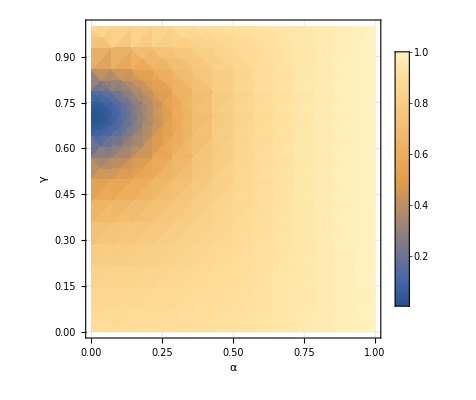

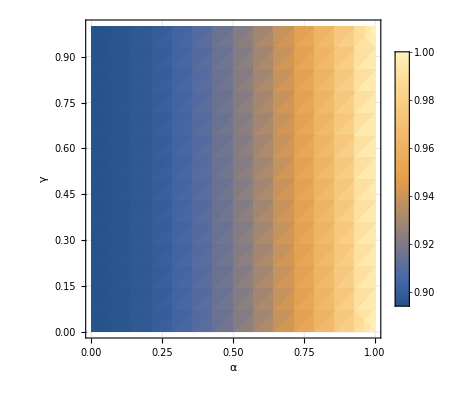

```mathematica
F[α_,γ_,ϕ_,η_]=1/(1+((1-α^2)(1-η))/16(19+10 γ √(1-γ^2)Cos[ϕ])/(1+2(α^2-(1-α^2))γ √(1-γ^2)Cos[ϕ]));
η=0.9;
newStyle[A_]:=A/.l_Line:>Sequence[Opacity[1],Thickness[.005],Red,l]
DensityPlot[ F[α,γ,0,η],{α,0,1},{γ,0,1},FrameLabel->Automatic,RotateLabel-> True,LabelStyle->Large,AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotRange->Full,ImageSize->Scaled[0.5],ColorFunctionScaling->True,PlotLegends->Automatic]
DensityPlot[ F[α,γ,π/2,η],{α,0,1},{γ,0,1},FrameLabel->Automatic,RotateLabel-> True,LabelStyle->Large,AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotRange->Full,ImageSize->Scaled[0.5],ColorFunctionScaling->True,PlotLegends->Automatic]/.Tooltip[A_,0.9]:>Tooltip[newStyle[A],0.9]
```